## BRDF Definitions

```mathematica
ggx[μ_,α_]:=α^2/(π(μ^2(α^2-1)+1)^2)
smith[θ_,α_]:=1/(Cos[θ]+√(α^2+(1-α^2)*Cos[θ]^2))
(* change[] gives cos(Subscript[θ, h]) when provided with Subscript[ω, i] and Subscript[ω, o] *)
change[θo_,θi_,ϕi_]:=(Cos[θo]+Cos[θi])/(√(2*(1+Cos[θo]*Cos[θi]+Sin[θo]*Sin[θi]*Cos[ϕi])))
oren=Function[ {θo,ϕo,θi,ϕi,α},
σ=π/2 α;
A = 1-0.5*σ^2/(σ^2+0.33);
B = 0.45*σ^2/(σ^2+0.09);
a=Max[θo,θi];
b=Min[θo,θi];
1/π(A+B*Max[0,Cos[ϕo-ϕi]]*Sin[a]*Tan[b])
];
```

## Tables Loading

### GGX

```mathematica
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 
countX=128;
countY=128;
resultEo = Import["MSBRDF_GGX_E128x128.csv","CSV"];
resultEavg=Import["MSBRDF_GGX_Eavg128.csv","CSV"];
fEo=ListInterpolation[Table[resultEo[[1+countX*(y-1)+(x-1)]][[3]],{x,1,countY},{y,1,countY}],{{0,1},{0,1}}]
fEavg=ListInterpolation[Table[resultEavg[[i]][[2]],{i,1,countY}],{0,1}]
Plot[fEavg[x],{x,0,1},PlotRange->{0,π}, AxesLabel->{"α","E_avg"}];
Plot3D[fEo[x,y],{x,0,1},{y,0,1},AxesLabel->{"cos(θ)", "α","E_i"}];

BRDFggx[θo_,θi_,ϕi_,α_]:= smith[θo,α]*smith[θi,α]*ggx[change[θo,θi,ϕi],α]
BRDFms[θo_,θi_,α_]:=((1-fEo[Cos[θo],α])*(1-fEo[Cos[θi],α]))/(π-fEavg[α])
fWhiteFurnaceSS[α_]:=2*π*NIntegrate[BRDFggx[θo,θi,ϕi,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
fWhiteFurnaceMS[α_]:=2*π*NIntegrate[BRDFms[θo,θi,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
fWhiteFurnaceSS[0.3]
fWhiteFurnaceMS[0.3]
π-fEavg[0.3]
fWhiteFurnaceSS[0.3]+fWhiteFurnaceMS[0.3]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

InterpolatingFunction[{{0., 1.}}, <>]

2.64771

0.493886

0.493886

3.14159

### Oren-Nayar

```mathematica
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 
countX=32;
countY=32;
resultOrenEo = Import["MSBRDF_OrenNayar_E32x32.csv","CSV"];
resultOrenEavg = Import["MSBRDF_OrenNayar_Eavg32.csv","CSV"];
fOrenEo=ListInterpolation[Table[resultOrenEo[[1+countX*(y-1)+(x-1)]][[3]],{x,1,countY},{y,1,countY}],{{0,1},{0,1}}]
fOrenEavg=ListInterpolation[Table[resultOrenEavg[[i]][[2]],{i,1,countY}],{0,1}]
Plot[fOrenEavg[x],{x,0,1},PlotRange->{0,π}, AxesLabel->{"α","E_avg"}];
Plot3D[fOrenEo[x,y],{x,0,1},{y,0,1},AxesLabel->{"cos(θ)", "α","E_i"}];

oren=Function[ {θo,ϕo,θi,ϕi,α},
σ=π/2 α;
A = 1-0.5*σ^2/(σ^2+0.33);
B = 0.45*σ^2/(σ^2+0.09);
a=Max[θo,θi];
b=Min[θo,θi];
1/π(A+B*Max[0,Cos[ϕo-ϕi]]*Sin[a]*Tan[b])
];
BRDForen[θo_,θi_,ϕ_,α_]:= oren[θo,0,θi,ϕ,α]
BRDForenms[θo_,θi_,ϕ_,α_]:=((1-fOrenEo[Cos[θo],α])*(1-fOrenEo[Cos[θi],α]))/(π-fOrenEavg[α])
fWhiteFurnaceSS[α_]:=2*π*NIntegrate[BRDForen[θo,θi,ϕi,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
fWhiteFurnaceMS[α_]:=2*π*NIntegrate[BRDForenms[θo,θi,ϕi,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
fWhiteFurnaceSS[0.3]
fWhiteFurnaceMS[0.3]
π-fOrenEavg[0.3]
fWhiteFurnaceSS[0.3]+fWhiteFurnaceMS[0.3]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

InterpolatingFunction[{{0., 1.}}, <>]

2.72499

0.416867

0.416867

3.14186

# SH Environment

We start by writing the expression we need to fit for various roughness values:

	∫_(Ω^+)^upper L(ω_i)  f(ω_o,ω_i) (ω_i· n)ⅆω  =∫_(Ω^+)^upper L(ω_i)  ((1-E(ω_o,α))(1-E(ω_i,α)))/(π-E_avg(α)) (ω_i· n)ⅆω
				=∫_(Ω^+)^upper (L_lm · Y_lm(ω_i))  ((1-E(ω_o,α))(1-E(ω_i,α)))/(π-E_avg(α)) (ω_i· n)ⅆω
				= L_lm  (1-E(ω_o,α))/(π-E_avg(α))∫_(Ω^+)^upper Y_lm(ω_i)(1-E(ω_i,α))(ω_i· n)ⅆω 
Where Y_lm(ω_i) is a spherical harmonics coefficient in the direction ω_i.
We notice that the integral is only dependent on roughness α and we will attempt to compute it for all values of (l,m) and various values of roughness to finally attempt to find a nice analytical fit for the coefficients for each BRDF.

```mathematica
SphericalPlot3D[Abs[Re[SphericalHarmonicY[1,-1,θ,ϕ]]],{θ,0,Pi},{ϕ,0,2Pi}]
```

-Graphics3D-

GGX Case

```mathematica
fSHBRDFggx= Function[ {i,θ,ϕ,α}, l=Floor[Sqrt[i]];m=i-l*(l+1); Re[SphericalHarmonicY[l,m,θ,ϕ]]*(1-fEo[Cos[θ],α])];
NIntegrate[fSHBRDFggx[2,θ,ϕ,0.5]*Cos[θ]*Sin[θ],{θ,0,π/2},{ϕ,-π,π}]
```

0.32273

```mathematica
(* Integration method & accuracy test *)
NIntegrate[fSHBRDFggx[1,θ,ϕ,α]*Cos[θ]*Sin[θ],{θ,0,π/2},{ϕ,-π,π},Method->"AdaptiveMonteCarlo",MaxRecursion->4, AccuracyGoal->4]
```

```mathematica
α=1
Table[NIntegrate[fSHBRDFggx[i,θ,ϕ,α]*Cos[θ]*Sin[θ],{θ,0,π/2},{ϕ,-π,π},Method->"AdaptiveMonteCarlo",MaxRecursion->4, AccuracyGoal->4],{i,0,8}]
```

Here I realized only the ZH coefficients yield non-zero values and the rest are useless! No need to bother computing all of them... :)

```mathematica
taResultSH=Table[Table[{α,NIntegrate[fSHBRDFggx[i,θ,ϕ,α]*Cos[θ]*Sin[θ],{θ,0,π/2},{ϕ,-π,π},Method->"AdaptiveMonteCarlo",MaxRecursion->4, AccuracyGoal->4]},{α,0.05,1,0.05}],{i,0,8}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {θ, ϕ} = {0.300983, 0.43966}. NIntegrate obtained -0.000172763 and 0.000341689 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ, ϕ} = {0.915842, 0.0752998}. NIntegrate obtained -0.0000293678 and 0.000234285 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ, ϕ} = {0.257175, 0.98731}. NIntegrate obtained 0.000164458 and 0.000563884 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{{{0.05,0.00785133},{0.1,0.0251353},{0.15,0.0483938},{0.2,0.0763309},{0.25,0.106231},{0.3,0.138373},{0.35,0.175404},{0.4,0.20676},{0.45,0.241341},{0.5,0.275056},{0.55,0.310735},{0.6,0.337177},{0.65,0.373458},{0.7,0.404508},{0.75,0.436621},{0.8,0.459355},{0.85,0.479699},{0.9,0.51428},{0.95,0.536335},{1.,0.544749}},{{0.05,-0.0000328025},{0.1,-1.96805×10^-8},{0.15,0.000111265},{0.2,0.000151473},{0.25,-0.000101461},{0.3,-0.0000391024},{0.35,0.0000771395},{0.4,-0.000166549},{0.45,-0.0000488318},{0.5,0.000096373},{0.55,0.0000292848},{0.6,-0.000172763},{0.65,-0.0000293678},{0.7,-0.000200802},{0.75,0.000164458},{0.8,-0.000113424},{0.85,-0.000299388},{0.9,1.42828×10^-6},{0.95,-0.000407988},{1.,0.0000917717}},{{0.05,0.00554451},{0.1,0.0215324},{0.15,0.0464662},{0.2,0.0781465},{0.25,0.115544},{0.3,0.152915},{0.35,0.195135},{0.4,0.239346},{0.45,0.279347},{0.5,0.325276},{0.55,0.3676},{0.6,0.402803},{0.65,0.439326},{0.7,0.481875},{0.75,0.507705},{0.8,0.54915},{0.85,0.578466},{0.9,0.597144},{0.95,0.639123},{1.,0.668141}},{{0.05,-6.15987×10^-6},{0.1,0.0000672591},{0.15,0.000039873},{0.2,0.0000561893},{0.25,-0.000135118},{0.3,-0.0000113104},{0.35,0.000018843},{0.4,0.0000479546},{0.45,-0.0000690099},{0.5,0.0000330576},{0.55,0.000545705},{0.6,-0.0000375146},{0.65,0.000075669},{0.7,0.0000987955},{0.75,-0.0000196921},{0.8,0.0000734719},{0.85,0.000185651},{0.9,0.0000393009},{0.95,0.00122013},{1.,0.000544847}},{{0.05,0.000185398},{0.1,-0.000152188},{0.15,-0.0000297713},{0.2,0.000140439},{0.25,-0.000328453},{0.3,-0.0000358531},{0.35,0.0000143881},{0.4,-0.000125165},{0.45,0.00011157},{0.5,-0.000181923},{0.55,0.0000869931},{0.6,-0.000103008},{0.65,0.000289476},{0.7,-0.000190359},{0.75,0.0000289983},{0.8,-0.000165463},{0.85,-0.0000934835},{0.9,-0.000239035},{0.95,-0.000265153},{1.,0.0000515275}},{{0.05,0.000110374},{0.1,0.000050161},{0.15,0.0000693484},{0.2,-0.000110943},{0.25,3.69849×10^-6},{0.3,-0.0000282186},{0.35,-0.0000348662},{0.4,0.0000319974},{0.45,8.64754×10^-6},{0.5,-0.000136862},{0.55,0.000166},{0.6,0.000287094},{0.65,0.00233839},{0.7,0.00108515},{0.75,0.0000120484},{0.8,1.26395×10^-6},{0.85,-8.66103×10^-6},{0.9,0.000166937},{0.95,-0.0000649739},{1.,0.000185056}},{{0.05,-0.00243726},{0.1,-0.00202555},{0.15,0.0048432},{0.2,0.0181753},{0.25,0.0362972},{0.3,0.0599408},{0.35,0.0854637},{0.4,0.108109},{0.45,0.135604},{0.5,0.163988},{0.55,0.189823},{0.6,0.211818},{0.65,0.234066},{0.7,0.254929},{0.75,0.282459},{0.8,0.296811},{0.85,0.313259},{0.9,0.329407},{0.95,0.348168},{1.,0.356641}},{{0.05,0.000102199},{0.1,-0.000144954},{0.15,0.0000217622},{0.2,-0.000362315},{0.25,0.0000895545},{0.3,0.000111607},{0.35,-0.0000213085},{0.4,0.0000306241},{0.45,-0.0000268153},{0.5,-0.000522498},{0.55,0.0000776233},{0.6,0.0000411729},{0.65,-0.000797604},{0.7,0.0000926268},{0.75,0.0000188132},{0.8,0.000390349},{0.85,0.000106747},{0.9,0.00025818},{0.95,-0.000450533},{1.,0.00118579}},{{0.05,-0.0000570671},{0.1,-0.000195735},{0.15,-0.0000753328},{0.2,-0.0000213601},{0.25,-0.00003109},{0.3,1.18372×10^-6},{0.35,-0.0000771683},{0.4,-1.32733×10^-6},{0.45,0.0000130281},{0.5,0.000165903},{0.55,0.000143518},{0.6,0.000830982},{0.65,0.000917881},{0.7,-0.0000640512},{0.75,-0.0000577116},{0.8,-0.0000599488},{0.85,0.0000292757},{0.9,-0.000326618},{0.95,0.000176153},{1.,0.0000535893}}}

We easily notice only the ZH coefficients are non zero, which is even better!

```mathematica
taResultSHGGX={taResultSH[[1]], taResultSH[[3]],taResultSH[[7]]}
```

{{{0.05,0.00785133},{0.1,0.0251353},{0.15,0.0483938},{0.2,0.0763309},{0.25,0.106231},{0.3,0.138373},{0.35,0.175404},{0.4,0.20676},{0.45,0.241341},{0.5,0.275056},{0.55,0.310735},{0.6,0.337177},{0.65,0.373458},{0.7,0.404508},{0.75,0.436621},{0.8,0.459355},{0.85,0.479699},{0.9,0.51428},{0.95,0.536335},{1.,0.544749}},{{0.05,0.00554451},{0.1,0.0215324},{0.15,0.0464662},{0.2,0.0781465},{0.25,0.115544},{0.3,0.152915},{0.35,0.195135},{0.4,0.239346},{0.45,0.279347},{0.5,0.325276},{0.55,0.3676},{0.6,0.402803},{0.65,0.439326},{0.7,0.481875},{0.75,0.507705},{0.8,0.54915},{0.85,0.578466},{0.9,0.597144},{0.95,0.639123},{1.,0.668141}},{{0.05,-0.00243726},{0.1,-0.00202555},{0.15,0.0048432},{0.2,0.0181753},{0.25,0.0362972},{0.3,0.0599408},{0.35,0.0854637},{0.4,0.108109},{0.45,0.135604},{0.5,0.163988},{0.55,0.189823},{0.6,0.211818},{0.65,0.234066},{0.7,0.254929},{0.75,0.282459},{0.8,0.296811},{0.85,0.313259},{0.9,0.329407},{0.95,0.348168},{1.,0.356641}}}

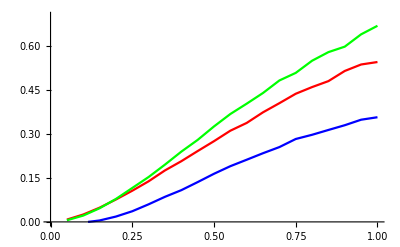

```mathematica
Show[Table[ListLinePlot[taResultSHGGX[[i]],PlotRange->{0,0.7},PlotStyle->Hue[(i-1)/3]],{i,1,3}]]
```

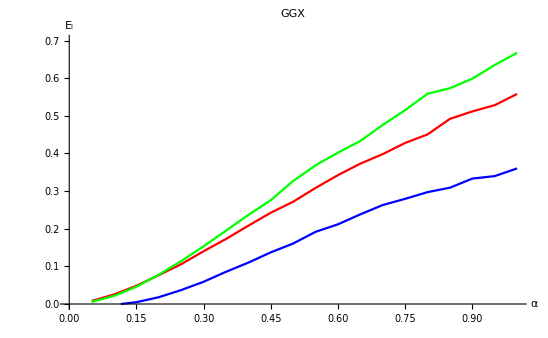

```mathematica
ZHindex={0,2,6};
taResultSHGGX=Table[Table[{α,2*π*NIntegrate[fSHBRDFggx[ZHindex[[i]],θ,0,α]*Cos[θ]*Sin[θ],{θ,0,π/2},Method->"AdaptiveMonteCarlo",MaxRecursion->8, AccuracyGoal->6]},{α,0.05,1,0.05}],{i,1,3}];
Show[Table[ListLinePlot[taResultSHGGX[[i]],PlotRange->{0,0.7},PlotStyle->Hue[(i-1)/3],AxesLabel->{"α","E_l"},PlotLabel->"GGX"],{i,1,3}]
]
```

Oren-Nayar Case

```mathematica
fSHBRDForen= Function[ {i,θ,ϕ,α}, l=Floor[Sqrt[i]];m=i-l*(l+1); Re[SphericalHarmonicY[l,m,θ,ϕ]]*(1-fOrenEo[Cos[θ],α])];
NIntegrate[fSHBRDForen[2,θ,ϕ,0.5]*Cos[θ]*Sin[θ],{θ,0,π/2},{ϕ,-π,π}]
NIntegrate[2*π*fSHBRDForen[2,θ,0,0.5]*Cos[θ]*Sin[θ],{θ,0,π/2}]
```

0.263663

0.263663

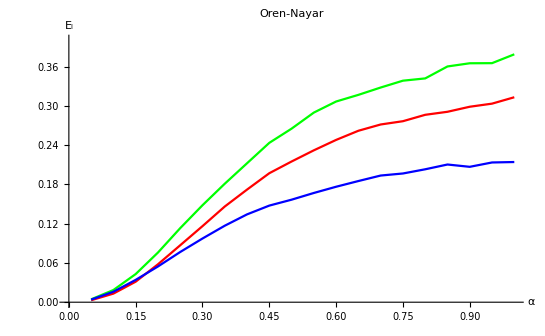

```mathematica
ZHindex={0,2,6};
taResultSHoren=Table[Table[{α,2*π*NIntegrate[fSHBRDForen[ZHindex[[i]],θ,0,α]*Cos[θ]*Sin[θ],{θ,0,π/2},Method->"AdaptiveMonteCarlo",MaxRecursion->8, AccuracyGoal->6]},{α,0.05,1,0.05}],{i,1,3}];
Show[Table[ListLinePlot[taResultSHoren[[i]],PlotRange->{0,0.4},PlotStyle->Hue[(i-1)/3],AxesLabel->{"α","E_l"},PlotLabel->"Oren-Nayar"],{i,1,3}]
]
```

## Fitting

{{a→-0.017923,b→1.05613,c→-0.48655,d→0.},{a→-0.0612744,b→1.33802,c→-0.619582,d→0.},{a→-0.107329,b→0.86862,c→-0.398001,d→0.}}

{Function[x,-0.017923 √x+1.05613 x^(3/2)-0.48655 x^(5/2)],Function[x,-0.0612744 √x+1.33802 x^(3/2)-0.619582 x^(5/2)],Function[x,-0.107329 √x+0.86862 x^(3/2)-0.398001 x^(5/2)]}

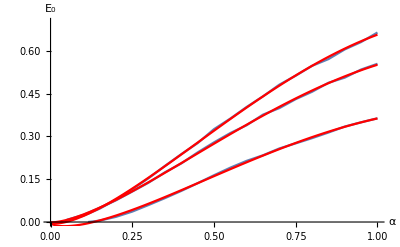

```mathematica
Clear[a,b,c,d,x]
fittingMethod="LevenbergMarquardt";
fittingMethod="PrincipalAxis";
fittingMethod="Automatic";

model=a*(1-(b*x+c*x^2+d*x^3));
model=a*x^(1/2)+b*x^(3/2)+c*x^(5/2)+d*x^(7/2);
model=a*x^(1/2)+b*x^(3/2)+c*x^(5/2);
fitGGX=Table[FindFit[taResultSHGGX[[i]],model,{a,b,c,d},x,Method->fittingMethod],{i,1,3}]
funcSHGGX=Table[Function[x,Evaluate[model/.fitGGX[[i]]]],{i,1,3}]
Show[
Table[ListLinePlot[taResultSHGGX[[i]],PlotRange->{0,0.7},AxesLabel->{"α","E_0"}],{i,1,3}],
Table[Plot[funcSHGGX[[i]][x],{x,0,1},PlotStyle->Red],{i,1,3}]
]
```

```mathematica
a->-0.017923032436367253,b->1.0561278339405598,c->-0.4865495717038784,d->0.},{a->-0.06127443169094851,b->1.3380225947779523,c->-0.6195823982255909,d->0.},{a->-0.10732852337149004,b->0.8686198207608287,c->-0.3980009298364805,d->0.
```

{{a→-0.0919559,b→1.46704,c→-1.67354,d→0.607801},{a→-0.113668,b→1.90127,c→-2.32232,d→0.909816},{a→-0.0412482,b→1.09335,c→-1.41719,d→0.581084}}

{Function[x,-0.0919559 √x+1.46704 x^(3/2)-1.67354 x^(5/2)+0.607801 x^(7/2)],Function[x,-0.113668 √x+1.90127 x^(3/2)-2.32232 x^(5/2)+0.909816 x^(7/2)],Function[x,-0.0412482 √x+1.09335 x^(3/2)-1.41719 x^(5/2)+0.581084 x^(7/2)]}

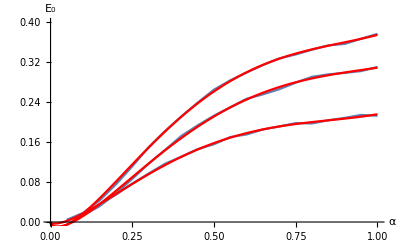

```mathematica
model=0*a+b*x+c*x^2+d*x^3+e*x^4;
model=a*x^(1/2)+b*x^(3/2)+c*x^(5/2)+d*x^(7/2);
fitOren=Table[FindFit[taResultSHoren[[i]],model,{a,b,c,d},x,Method->fittingMethod],{i,1,3}]
funcSHOren=Table[Function[x,Evaluate[model/.fitOren[[i]]]],{i,1,3}]
Show[
Table[ListLinePlot[taResultSHoren[[i]],PlotRange->{0,0.4},AxesLabel->{"α","E_0"}],{i,1,3}],
Table[Plot[funcSHOren[[i]][x],{x,0,1},PlotStyle->Red],{i,1,3}]
]
```

```mathematica
{a->-0.0919559140506979,b->1.467037714315657,c->-1.6735448883797404,d->0.607800523815945},{a->-0.11366841288600084,b->1.901273744271233,c->-2.322322430339633,d->0.909815621695672},{a->-0.04124821752212919,b->1.0933549500536324,c->-1.4171919237898756,d->0.5810844359893627}
```